```mathematica
holo=((RNA0-holo)*(L0-holo))/Kbind
```

```mathematica
Solve[((RNA0-holo)*(L0-holo))/Kbind==holo,holo]
```

{{holo→1/2 (Kbind+L0+RNA0-√((-Kbind-L0-RNA0)^2-4 L0 RNA0))},{holo→1/2 (Kbind+L0+RNA0+√((-Kbind-L0-RNA0)^2-4 L0 RNA0))}}

```mathematica
holo1[L0_,RNA0_,Kbind_]:=((1/2 (Kbind+L0+RNA0-√((-Kbind-L0-RNA0)^2-4 L0 RNA0)))/RNA0)*100
holo2[L0_,RNA0_,Kbind_]:=((1/2 (Kbind+L0+RNA0+√((-Kbind-L0-RNA0)^2-4 L0 RNA0)))/RNA0)*100
```

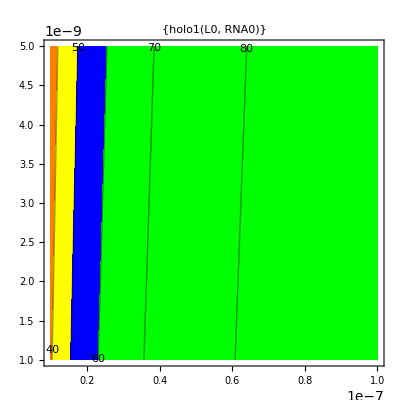

-Graphics-

```mathematica
ContourPlot[holo1[L0,RNA0,1.5*10^-8],{L0,0.01*10^-6,0.1*10^-6},{RNA0,1*10^-9,5*10^-9},Contours->{10,20,30,40,50,60,70,80,90,100},ContourShading->{Red,Red,Red,Orange,Yellow,Blue,Green,Green,Green,Green},ContourLabels->True,PlotLabel->{"holo1(L0, RNA0)"},PlotRange->{0,100}]
ContourPlot[holo2[L0,RNA0,1.5*10^-8],{L0,0.01*10^-6,0.1*10^-6},{RNA0,1*10^-9,5*10^-9},Contours->{10,20,30,40,50,60,70,80,90,100},ContourShading->{Red,Red,Red,Orange,Yellow,Blue,Green,Green,Green,Green},ContourLabels->True,PlotLabel->{"holo2(L0, RNA0)"},PlotRange->{0,100}]
```

```mathematica
R=8.3144621 (*J/mol*K*)
DeltaHbind=110470.2357608338
DeltaSbind=238.303284932985
holo[L0_,RNA0_,T_]:=((1/2 (ⅇ^(-(DeltaHbind-T*DeltaSbind)/(R*T))+L0+RNA0-√((-ⅇ^(-(DeltaHbind-T*DeltaSbind)/(R*T))-L0-RNA0)^2-4 L0 RNA0)))/RNA0)*100
```

8.31446

110470.

238.303

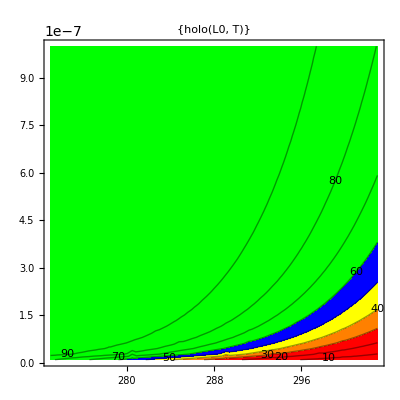

Plot::prng: Value of option PlotRange -> {0, 100} . PlotStyle → RGBColor[0, 0, 1] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

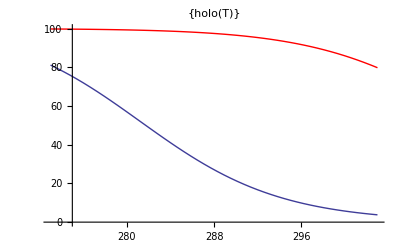

```mathematica
ContourPlot[holo[L0,1.5*10^-9,T],{T,273,303},{L0,0.01*10^-6,1*10^-6},Contours->{10,20,30,40,50,60,70,80,90,100},ContourShading->{Red,Red,Red,Orange,Yellow,Blue,Green,Green,Green,Green},ContourLabels->True,PlotLabel->{"holo(L0, T)"},PlotRange->{0,100}]
p1=Plot[holo[1*10^-6,1.5*10^-9,T],{T,273,303},PlotLabel->{"holo(T)"},PlotRange->{0,100},PlotStyle->Red];
p2=Plot[holo[0.01*10^-6,1.5*10^-9,T],{T,273,303},PlotLabel->{"holo(T)"},PlotRange->{0,100}.PlotStyle->Blue];
Show[p1,p2]
```

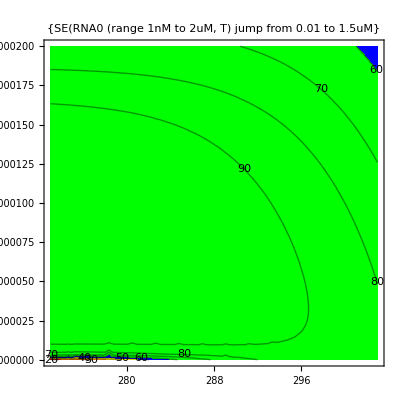

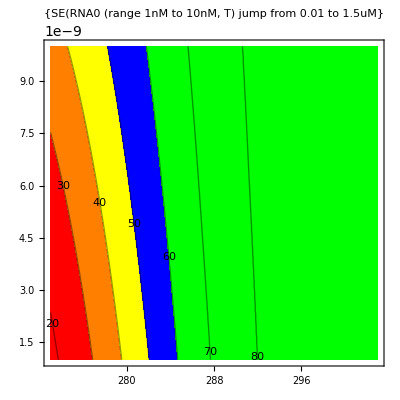

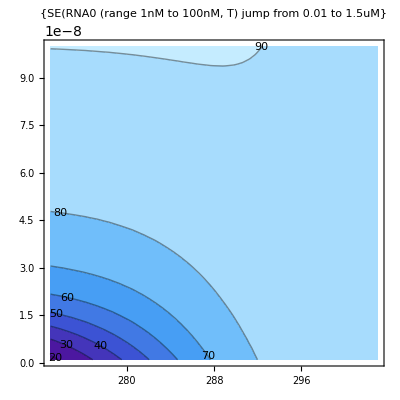

```mathematica
ContourPlot[holo[1.5*10^-6,RNA0,T]-holo[0.01*10^-6,RNA0,T],{T,273,303},{RNA0,1*10^-9,2*10^-6},Contours->{10,20,30,40,50,60,70,80,90,100},ContourShading->{Red,Red,Red,Orange,Yellow,Blue,Green,Green,Green,Green},ContourLabels->True,PlotLabel->{"SE(RNA0 (range 1nM to 2uM, T) jump from 0.01 to 1.5uM"},PlotRange->{0,100}]
ContourPlot[holo[1.5*10^-6,RNA0,T]-holo[0.01*10^-6,RNA0,T],{T,273,303},{RNA0,1*10^-9,1*10^-8},Contours->{10,20,30,40,50,60,70,80,90,100},ContourShading->{Red,Red,Red,Orange,Yellow,Blue,Green,Green,Green,Green},ContourLabels->True,PlotLabel->{"SE(RNA0 (range 1nM to 10nM, T) jump from 0.01 to 1.5uM"},PlotRange->{0,100}]
ContourPlot[holo[1.5*10^-6,RNA0,T]-holo[0.01*10^-6,RNA0,T],{T,273,303},{RNA0,1*10^-9,1*10^-7},
Contours->{10,20,30,40,50,60,70,80,90,100},ColorFunction->ColorData["DeepSeaColors"],ContourLabels->True,PlotLabel->{"SE(RNA0 (range 1nM to 100nM, T) jump from 0.01 to 1.5uM"},PlotRange->{0,100}]
```

8.31446

132703.

370.029

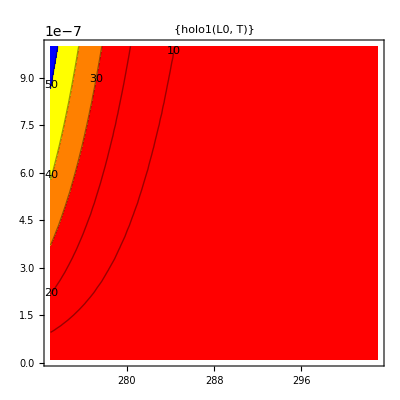

Plot::prng: Value of option PlotRange -> {0, 100} . PlotStyle → RGBColor[0, 0, 1] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

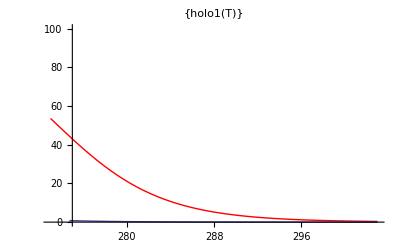

```mathematica
(*Werte für die NMR Magnesium Bedingungen*)
R=8.3144621 (*J/mol*K*)
DeltaHbind=132703.18846113922
DeltaSbind=370.02936714423925
holo[L0_,RNA0_,T_]:=((1/2 (ⅇ^(-(DeltaHbind-T*DeltaSbind)/(R*T))+L0+RNA0-√((-ⅇ^(-(DeltaHbind-T*DeltaSbind)/(R*T))-L0-RNA0)^2-4 L0 RNA0)))/RNA0)*100
ContourPlot[holo1[L0,1.5*10^-9,T],{T,273,303},{L0,0.01*10^-6,1*10^-6},Contours->{10,20,30,40,50,60,70,80,90,100},ContourShading->{Red,Red,Red,Orange,Yellow,Blue,Green,Green,Green,Green},ContourLabels->True,PlotLabel->{"holo1(L0, T)"},PlotRange->{0,100}]
p1=Plot[holo1[1*10^-6,1.5*10^-9,T],{T,273,303},PlotLabel->{"holo1(T)"},PlotRange->{0,100},PlotStyle->Red];
p2=Plot[holo1[0.01*10^-6,1.5*10^-9,T],{T,273,303},PlotLabel->{"holo1(T)"},PlotRange->{0,100}.PlotStyle->Blue];
Show[p1,p2]
```